```mathematica
Databin["EM6FHeXi", -10]
```

Databin[…]

```mathematica
mostRecent=Normal[Dataset[Databin["EM6FHeXi", -10]]];
```

```mathematica
mostRecent[[All,1,-1]]
```

{5e0c43cac3c9f0a1764ef8ce1835ae2d6b68e54ee57fe12831f87392fcf2bcfe,dabe1191f360e3c092757abaabca961bc1268d337d67ec9ba5fa1ce74f39c506,a081ed14e7095689b306fc198b501ea89553d1c6d1494b30043828fbdc657ac4,dfe006ec306beac11ea2b3c5e1a18e729d9b47782067d2b3cfda42ba9463f22a,f9e2762f0c947a9d28a856afc31e18687b52a14bbce8694f3cff4a66bd50fc0e,d629902235951dd608ae1dff4ab271d1204a3b545484907ee5c7e7765259af09,754531a06a90ec41db89b59399187e1b25b725ba16acd1bdf08a0aab75b5d475,6938d829009e66cb0c4d063d71a397ba769a0953fdd817e1060c63edd72267fd,ec3a8dfeb435754ae35ba7a006c79168056c58094302c1887773bcc3d95c4965,6063b086d7975b826909ec82d5b8be2930c4e55199c1631908e1d27062b5ac3c}

```mathematica
data2=Dataset[BlockchainGet[mostRecent[[All,1,-1]]]]
```

Dataset[<>]

```mathematica
temps=data2[[1;;All,2,1,1,2]]//Normal
```

{70.7 °F,70.3 °F,69.4 °F,68.9 °F,67.8 °F,67.3 °F,71.8 °F,73.6 °F,75.7 °F,77.7 °F}

```mathematica
times=data2[[1;;All,2,2]]//Normal
```

{Sun 7 Jul 2019 03:16:07GMT-4.,Sun 7 Jul 2019 04:16:07GMT-4.,Sun 7 Jul 2019 05:16:07GMT-4.,Sun 7 Jul 2019 06:16:07GMT-4.,Sun 7 Jul 2019 07:16:06GMT-4.,Sun 7 Jul 2019 08:16:06GMT-4.,Sun 7 Jul 2019 09:16:07GMT-4.,Sun 7 Jul 2019 10:16:07GMT-4.,Sun 7 Jul 2019 11:16:06GMT-4.,Sun 7 Jul 2019 12:16:07GMT-4.}

```mathematica
ToExpression@First@First@temps//InputForm
```

70.7

```mathematica
MapAt[ToExpression,First@temps,1]//InputForm
```

Quantity[70.7, "DegreesFahrenheit"]

{{Sun 7 Jul 2019 03:16:07GMT-4.,70.7 °F},{Sun 7 Jul 2019 04:16:07GMT-4.,70.3 °F},{Sun 7 Jul 2019 05:16:07GMT-4.,69.4 °F},{Sun 7 Jul 2019 06:16:07GMT-4.,68.9 °F},{Sun 7 Jul 2019 07:16:06GMT-4.,67.8 °F},{Sun 7 Jul 2019 08:16:06GMT-4.,67.3 °F},{Sun 7 Jul 2019 09:16:07GMT-4.,71.8 °F},{Sun 7 Jul 2019 10:16:07GMT-4.,73.6 °F},{Sun 7 Jul 2019 11:16:06GMT-4.,75.7 °F},{Sun 7 Jul 2019 12:16:07GMT-4.,77.7 °F}}

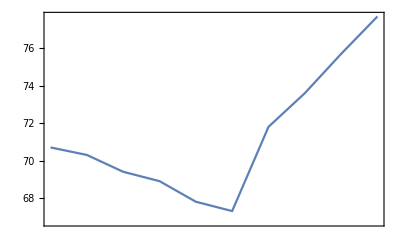

```mathematica
DateListPlot[Echo@Transpose[{times, MapAt[ToExpression,#,1]&/@temps}]]
```

```mathematica
DateListPlot[times, MapAt[ToExpression,#,1]&/@temps]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {DateObject[{2019,7,7,3,16,7.},Instant,Gregorian,-4.],DateObject[{2019,7,7,4,16,7.},Instant,Gregorian,-4.],«6»,DateObject[{2019,7,7,11,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,7,12,16,7.},Instant,Gregorian,-4.]} is not a valid dataset or list of datasets.

DateListPlot[{Sun 7 Jul 2019 03:16:07GMT-4.,Sun 7 Jul 2019 04:16:07GMT-4.,Sun 7 Jul 2019 05:16:07GMT-4.,Sun 7 Jul 2019 06:16:07GMT-4.,Sun 7 Jul 2019 07:16:06GMT-4.,Sun 7 Jul 2019 08:16:06GMT-4.,Sun 7 Jul 2019 09:16:07GMT-4.,Sun 7 Jul 2019 10:16:07GMT-4.,Sun 7 Jul 2019 11:16:06GMT-4.,Sun 7 Jul 2019 12:16:07GMT-4.},{70.7 °F,70.3 °F,69.4 °F,68.9 °F,67.8 °F,67.3 °F,71.8 °F,73.6 °F,75.7 °F,77.7 °F}]

```mathematica
data2[[1;;All,2,1,2]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,3]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,4]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,7]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,8]]
```

Dataset[<>]